Mohamed M. Hammad

Neural Network and Deep Learning with Mathematica                              < >    Ξ

Edited by Hao Feng

## 4 Multilayer Feed-Forward Neural Network

Remark:
This chapter provides a Mathematica implementation of the concepts and ideas presented in Chapter 3,  of the book titled Artificial Neural Network and Deep Learning: Fundamentals and Theory. We strongly recommend that you begin with the theoretical chapter to build a solid foundation before exploring the corresponding practical implementation.

In the rapidly evolving landscape of AI and machine learning [24-39], Feed-Forward Neural Networks (FFNNs) stand out as foundational structures, powering a multitude of applications across various domains. This chapter serves as a comprehensive introduction to the inner workings of FFNNs, delving into essential concepts and mechanisms crucial for understanding their functionality and effectiveness. We will start by looking at the structure of a FFNN, followed by how they are trained and used for making predictions. We will also take a brief look at the loss functions that should be used in different settings, the Activation Functions (AFs) used within a neuron, and the different types of optimizers that could be used for training.

The training process is a crucial phase in the development of FFNNs, enabling them to learn from data and improve their performance over time. The training procedure can be broken down into two main components, each playing a distinct role in the network’s learning process (forward propagation and back propagation).

We begin with an exploration of forward propagation in NNs, elucidating how input data traverse through the network’s layers to produce output predictions. Through a step-by-step examination, readers will grasp the fundamental principles underlying the propagation of information within these intricate systems.

A pivotal aspect of NN training is automatic differentiation and its main modes [40-43]. Automatic differentiation illustrates the mechanisms through which gradients are computed efficiently, enabling the network to adapt and optimize its parameters during the learning process. We further explore the training process and loss/cost functions integral to optimizing NNs. From defining objectives through appropriate loss functions to navigating the landscape of optimization algorithms.

We shift our focus to the backward pass, often referred to as Back Propagation (BP). During this phase, the network evaluates the error or the disparity between its predictions (outputs) and the actual target values. This discrepancy serves as a guide for adjusting the network’s weights to minimize the error and enhance its accuracy. BP involves traversing the network in reverse, updating weights based on the calculated error and its gradients.

Moreover, we explore the Universal Approximation Theorem (UAT) [44-46], which asserts that a FFNN with a single hidden layer can approximate any continuous function on a compact subset of ℝ𝑛. This theorem underscores the remarkable flexibility and potential of NNs in modeling complex, non-linear relationships.

In this chapter, we focus on the practical aspects of constructing NNs using Mathematica. We explore a variety of essential components and techniques for building NNs, ranging from fundamental layers to complex architectures.

• First, we will delve into the intricacies of constructing NNs from scratch using Mathematica. By exploring the foundational elements and step-by-step processes, you’ll gain a comprehensive understanding of NN architecture, training methodologies, and performance optimization.

• Next, we begin by understanding the foundational building block of NNs, the LinearLayer. This layer performs linear transformations on the input data, playing a crucial role in connecting different layers of the network. The key components of a LinearLayer are the weights and biases. During the training process, these parameters are adjusted iteratively using optimization algorithms such as gradient descent, enabling the network to learn from the data. The number of input features and the number of neurons in the LinearLayer determine the dimensions of the weight matrix.

• As we progress, we introduce the ElementwiseLayer, which enables element-wise operations such as ReLU AF or sigmoid activation across the network’s neurons. This layer adds non-linearity to the network, allowing it to learn complex patterns in the data. Mathematica provides options for customizing ElementwiseLayers, such as choosing different AFs, or defining custom AFs, allowing practitioners to tailor the behavior of ElementwiseLayers according to the specific requirements of their tasks.

• We explore two essential constructs for organizing NN architectures: NetChain and NetGraph. NetChain enables the sequential composition of layers, where the output of one layer serves as the input to the next layer. This sequential arrangement facilitates the construction of straightforward feedforward NN architectures, where data flows from input to output through a series of transformations. Creating a NetChain in Mathematica involves specifying the layers and their configurations sequentially.

• NetGraph is a powerful construct in Mathematica for building NN architectures that involve non-sequential or more complex connectivity patterns. Unlike NetChain, which represents a linear sequence of layers, NetGraph allows for the creation of arbitrary computational graphs, enabling the design of intricate NN structures. NetGraph enables the creation of NNs with arbitrary connectivity patterns, where layers can be connected in any configuration, including branching, merging, looping, and skip connections. This flexibility allows for the construction of sophisticated architectures tailored to specific tasks. NN architectures built using NetGraph are represented as directed graphs, where nodes represent layers or operations, and edges represent the flow of data between them.

• A crucial step in NN construction is initializing the network’s parameters. We discuss NetInitialize, a function in Mathematica that initializes these parameters, setting the stage for efficient training. Mathematica provides various initialization methods that can be specified through options in NetInitialize. These methods include “Random”, “Xavier”, “He”, and custom initialization functions.

• To quantify the performance of our NN models, we introduce loss functions. MeanSquaredLossLayer and MeanAbsoluteLossLayer are commonly used for regression tasks, measuring the difference between predicted and actual values. For classification problems, we explore the CrossEntropyLossLayer, a widely used loss function that measures the dissimilarity between predicted and actual class distributions.

• Finally, we conclude by discussing NetTrain, an essential function in Mathematica for training NNs. Under the hood, NetTrain employs gradient descent optimization algorithms, such as “SGD”,”ADAM” or “RMSProp” and “SignSGD”, to update the parameters of the NN iteratively.

Throughout this chapter, we provide insights and practical examples to empower readers in harnessing the capabilities of Mathematica for constructing, training, and fine-tuning NNs for various machine learning tasks.

### Building Neural Network from Scratch with Mathematica and Universal Approximation Theorem

In this unit, let us leverage Mathematica’s powerful features to implement a NN from scratch, train it on a regression task, perform forward and backward propagation, and visualize the training process and results. Implementing a NN from scratch is an invaluable exercise for deepening your understanding of how NNs work. By building a NN from the ground up, you gain insights into the inner workings of the algorithms involved, including forward and backward propagation, gradient descent optimization, weight initialization, AFs, and more. Building a NN from scratch helps you develop strong debugging skills. When you encounter errors or unexpected behavior, you’ll learn to diagnose and fix issues by tracing through the code and understanding how each component interacts.

Mathematica code 4.1 serves as an educational tool to implement the theoretical equations involved in training a NN for regression tasks. It is implementing a NN to approximate the function 𝑓(𝑥, 𝑦)=𝑥^2 +𝑦^2 . By implementing these theoretical equations in a practical coding environment, the code enables you to gain hands-on experience with training NNs.

The code demonstrates how to perform forward propagation through the NN layers. It illustrates the calculation of pre-activation and post-activation values for each layer, showcasing how information flows through the network. Backpropagation, which involves computing gradients of the loss function with respect to the weights and biases of each layer, is a fundamental aspect of training NNs. The code meticulously calculates these gradients, enabling you to understand the mathematics behind backpropagation.

Below are the main steps of the code:

1. Generate a set of training data points by evaluating the function 𝑓(𝑥, 𝑦) over a range of 𝑥 and 𝑦 values.

2. Define the architecture of the NN with three layers: an input layer with two neurons (for 𝑥 and 𝑦), two hidden layers with 10 neurons each, and an output layer with one neuron.

3. Initialize weights and biases randomly for each layer of the NN.

4. Define the hyperbolic tangent (tanh) AF and its derivative for use in the NN.

5. Implement forward propagation to compute the outputs of each layer in the NN for a given set of input data.

6. Plot 3D plots for the training data and the output of the NN before training. Also, create histograms to visualize the distributions of outputs from each layer of the NN before training.

7. Define the mean squared error (MSE) loss function to quantify the difference between the predicted outputs of the NN and the actual outputs.

8. Set the learning rate and the number of epochs for training the NN.

9. Iterate through the training data for the specified number of epochs. In each epoch:

▪ Perform forward propagation to compute the outputs of each layer.

▪ Calculate the loss using the defined loss function.

▪ Perform backpropagation to compute gradients of the loss with respect to the weights and biases of each layer.

▪ After computing gradients, the weights and biases of each layer are updated using gradient descent to minimize the loss function.

▪ The training loop continues until a stopping criterion is met. In this case, the loop stops either when the specified number of epochs is reached or when the loss falls below a certain threshold (0.0001 in this code).

10. The training progress is monitored by recording the loss at each epoch. This information is used to create a plot showing how the loss decreases over epochs, providing insight into the training performance.

11. Plot 3D plots for the training data and the output of the NN after training. Also, create histograms to visualize the distributions of outputs from each layer of the NN after training.

12. The code utilizes matrix-matrix multiplication for both forward and backward propagation. In forward propagation, it performs the matrix multiplication operation between the input matrices, typically representing the input features and weights of a neural network layer, to produce the output activations. These activations are then passed through AFs to compute the final output of the layer.

13. During backward propagation, the code computes the gradients of the loss function with respect to the input matrices using the chain rule of calculus. It propagates the gradients backwards, adjusting the weights of the network based on the computed gradients to minimize the loss.

While the code implements a basic FFNN and performs adequately for this simple function approximation task, there are several potential improvements that could be made, such as experimenting with different network architectures, AFs, learning rates, and optimization algorithms to improve training performance and convergence speed. Next chapters will provide an in-depth exploration of these subjects.

In Mathematica, Mathematica code 4.1 can be significantly condensed using Mathematica’s framework, reducing it to just a few lines, see Mathematica code 4.2. Units 4.2-4.6 will delve into the extensive capabilities of Mathematica’s NN framework, which offers a rich array of functions and tools for the precise definition, efficient training, and seamless deployment of NNs. The Wolfram Language offers advanced capabilities for the representation, construction, training and deployment of NNs. A large variety of layer types is available for symbolic composition and manipulation. Thanks to dedicated encoders and decoders, diverse data types such as image, text and audio can be used as input and output, deepening the integration with the rest of the Wolfram Language. It combines ease of use with advanced capabilities, making it suitable for both beginners and experts in deep learning.

code 4.1

(* The code demonstrates the training of a neural network to approximate the function f(x,y)=x^2+y^2. It begins by generating a dataset through the evaluation of this function across a specified range of x and y values. Following this, a neural network architecture is defined, comprising an input layer with 2 neurons, two hidden layers each with 10 neurons, and an output layer with 1 neuron. Initialization of network parameters involves randomly assigning weights and biases from a normal distribution. Through forward propagation, the network computes outputs for each layer based on the input data, while backpropagation facilitates gradient computation for parameter updates. The training loop iterates through multiple epochs, refining the network parameters via gradient descent to minimize the Mean Squared Error loss between predicted and actual outputs. Visualization techniques are employed to depict training progress and evaluate the network’s performance pre- and post-training through 3D plots and histograms: *)

{-Graphics3D-,-Graphics3D-}

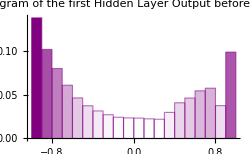
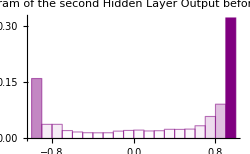
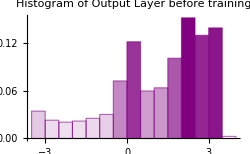

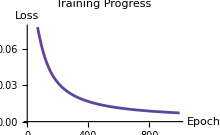

{-Graphics3D-,-Graphics3D-}

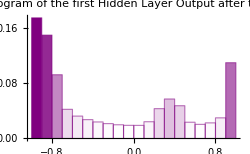
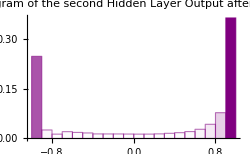
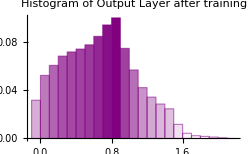

```mathematica
f[x_,y_]:=x^2+y^2;

xValues=Table[x,{x,-1,1,0.01}];
yValues=Table[y,{y,-1,1,0.01}];

trainingData=Flatten[
Table[
{x,y,f[x,y]},
{x,xValues},
{y,yValues}
],1];

m=Length[trainingData];

inputData=Transpose[trainingData[[All,1;;2]]];
outputData={trainingData[[All,3]]};

(*Neural network architecture:*)
numL=3; (*Number of layers.*)
n0=2; (*Number of neurons in input layer.*)
n1=10; (*Number of neurons in hidden layer 1.*)
n2=10; (*Number of neurons in hidden layer 2.*)
n3=1; (*Number of neurons in output layer.*)

SeedRandom[123];
weights1=RandomVariate[NormalDistribution[0,1],{n1,n0}];
biases1=Transpose[{RandomVariate[NormalDistribution[0,1],n1]}];
biasesmatrix1=Transpose[Table[Flatten[biases1],m]];

weights2=RandomVariate[NormalDistribution[0,1],{n2,n1}];
biases2=Transpose[{RandomVariate[NormalDistribution[0,1],n2]}];
biasesmatrix2=Transpose[Table[Flatten[biases2],m]];

weights3=RandomVariate[NormalDistribution[0,1],{n3,n2}];
biases3=Transpose[{RandomVariate[NormalDistribution[0,1],n3]}];
biasesmatrix3=Transpose[Table[Flatten[biases3],m]];

tanhActivation[x_]:=Tanh[x]

tanhDerivative[x_]:=1-Tanh[x]^2

forwardPropagation[inputs_]:=Module[
{preActivlayer1,postActivlayer1,preActivlayer2,postActivlayer2,preActivlayer3,postActivlayer3},

preActivlayer1=(weights1.inputs+biasesmatrix1);
postActivlayer1=Map[tanhActivation,preActivlayer1];

preActivlayer2=(weights2.postActivlayer1+biasesmatrix2);
postActivlayer2=Map[tanhActivation,preActivlayer2];

preActivlayer3=(weights3.postActivlayer2+biasesmatrix3);
postActivlayer3=preActivlayer3;

{preActivlayer1,postActivlayer1,preActivlayer2,postActivlayer2,preActivlayer3,postActivlayer3}
];

{preActivlayer1,layer1Output,preActivlayer2,layer2Output,preActivlayer3,layer3Output}=forwardPropagation[inputData];

NNOutPutData=Transpose[Join[inputData,layer3Output]];

Table[
ListPlot3D[
data[[2]],
PlotLabel->Style[Row[{"3D plot for ",data[[1]]}]],
ColorFunction->"Rainbow",
ImageSize->220
],
{data,{{"training Data \n before training",trainingData},{"NN output data \n before training",NNOutPutData}}}
]

Table[
Histogram[
Flatten[layer[[2]]],
Automatic,
"Probability",
PlotLabel->Style[Row[{"Histogram of ",layer[[1]]}]],
FrameLabel->{"Output","Probability"},
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple,
ImageSize->250
],
{layer,
{
{"the first Hidden Layer \n Output before training",layer1Output},
{"the second Hidden Layer \n Output before training",layer2Output},
{"Output Layer \n before training",layer3Output}
}
}
]

mseLoss[yActual_,yPredicted_]:=Mean[Flatten[(yPredicted-yActual)^2]]

learningRate=0.1;
numEpochs=1000;

Do[
{preActivlayer1,layer1Output,preActivlayer2,layer2Output,preActivlayer3,layer3Output}=forwardPropagation[inputData];

currentLoss=mseLoss[outputData,layer3Output];

delta3=(layer3Output-outputData);
gradWeights3=(1/m)*delta3.Transpose[layer2Output];
gradBiases3=(1/m)*{{Total[Flatten[delta3]]}};

delta2=(Transpose[weights3].delta3)*Map[tanhDerivative,preActivlayer2];
gradWeights2=(1/m)*delta2.Transpose[layer1Output];
gradBiases2=(1/m)*Transpose[{Total[Transpose[delta2]]}];

delta1=(Transpose[weights2].delta2)*Map[tanhDerivative,preActivlayer1];
gradWeights1=(1/m)*delta1.Transpose[inputData];
gradBiases1=(1/m)*Transpose[{Total[Transpose[delta1]]}];

weights3=weights3-learningRate*gradWeights3;
biases3=biases3-learningRate*gradBiases3;
biasesmatrix3=Transpose[Table[Flatten[biases3],m]];

weights2=weights2-learningRate*gradWeights2;
biases2=biases2-learningRate*gradBiases2;
biasesmatrix2=Transpose[Table[Flatten[biases2],m]];

weights1=weights1-learningRate*gradWeights1;
biases1=biases1-learningRate*gradBiases1;
biasesmatrix1=Transpose[Table[Flatten[biases1],m]];

lastEpoch=epoch;
trainingprogress[epoch]={epoch,currentLoss};
If[currenLoss<0.0001,Break[]];,
{epoch,numEpochs}
];

ListPlot[
Table[trainingprogress[i],{i,1,lastEpoch}],
PlotLabel->"Training Progress",
AxesLabel->{"Epoch","Loss"},
Joined->True,
ColorFunction->"Rainbow",
ImageSize->220
]

{preActivlayer1n,layer1Outputn,preActivlayer2n,layer2Outputn,preActivlayer3n,layer3Outputn}=forwardPropagation[inputData];

NNOutPutDatan=Transpose[Join[inputData,layer3Outputn]];

Table[
ListPlot3D[
data[[2]],
PlotLabel->Style[Row[{"3D plot for ",data[[1]]}]],
ColorFunction->"Rainbow",
ImageSize->220
],
{data,{{"training Data \n after training",trainingData},{"output data \n after training",NNOutPutDatan}}}
]

Table[
Histogram[
Flatten[layer[[2]]],
Automatic,
"Probability",
PlotLabel->Style[Row[{"Histogram of ",layer[[1]]}]],
FrameLabel->{"Output","Probability"},
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple,
ImageSize->250
],
{layer,
{
{"the first Hidden Layer \n Output after training",layer1Outputn},
{"the second Hidden Layer \n Output after training",layer2Outputn},
{"Output Layer \n after training",layer3Outputn}
}
}
]
```

code 4.2

(* The code demonstrates training a neural network to approximate a given function and visualizing the learned function’s surface. The code aims to achieve the following: Generate a dataset consisting of input-output pairs where the inputs are coordinates (x,y) and the outputs are the result of the function x^2+y^2. Construct a neural network architecture with two hidden layers, each containing 10 neurons with hyperbolic tangent activation functions, and an output layer with a single neuron. Train the neural network using the generated dataset to learn the relationship between the input coordinates and the corresponding function values. Visualize the learned function by plotting its 3D surface over a specified range of x and y values: *)

```mathematica
data=Flatten@Table[
{x,y}->x^2+y^2,
{x,-1,1,0.01},
{y,-1,1,0.01}
];

neuralNet=NetChain[{10,Tanh,10,Tanh,1}];
trainedNet=NetTrain[neuralNet,data,BatchSize->1024]

Plot3D[
trainedNet[{x,y}],
{x,-2,2},
{y,-2,2},
NormalsFunction->None,
ColorFunction->"Rainbow",
ImageSize->220]
```

Comparing SGD and Full batch Gradient Descent (FBGD) provides insights into their respective strengths and weaknesses. The goal of the Mathematica Code 4.3 and Mathematica Code 4.4 are to implement FBGD and SGD, respectively, for linear regression using basic NN with a single neuron, one input, and one bias term.

Below are the main steps of Mathematica Code 4.3:

1. Define a cost function that measures the squared error between the predicted values and the actual values of the dataset.

2. Define the gradient of the cost function with respect to the model parameters (weights and bias) using the chain rule of differentiation.

3. Implement a FBGD algorithm that updates the model parameters using the gradients computed over the entire dataset at each iteration.

4. Visualize the linear regression model fitted to the dataset after running FBGD. This includes plotting the dataset and the regression line.

5. Plot the magnitude of the gradients over the iterations to observe the convergence behavior of the optimization algorithm.

6. Plot the gradients of the cost function with respect to the model parameters (weights and bias) over the iterations to understand how they change during optimization.

7. Plot the value of the cost function over the iterations to monitor the optimization progress and convergence.

8. Plot the values of the model parameters (weights and bias) over the iterations to observe how they change during optimization.

In comparison to SGD, Mathematica Code 4.4, which updates the model parameters using gradients computed from individual data points randomly sampled from the dataset, FBGD computes gradients using the entire dataset, Mathematica Code 4.3. This fundamental difference in sampling methodology leads to distinct convergence behaviors between the two optimization algorithms.

For example, the figure “Cost Function over 1000 Iterations”, Mathematica Code 4.3, for FBGD typically shows smoother convergence compared to SGD, Mathematica Code 4.4, where the cost function tends to exhibit more fluctuations due to the randomness in selecting individual data points for computing gradients. While SGD can sometimes converge faster due to more frequent parameter updates, FBGD often provides more stable convergence and a smoother decrease in the cost function. However, FBGD may be computationally more expensive since it requires processing the entire dataset at each iteration.

In FBGD, the entire training dataset is used to compute the gradient of the cost function in each iteration. As a result, the cost function surface remains static throughout the training process since the gradient is calculated using all data points at once. Therefore, the plot displays a single static error surface. On the other hand, for SGD, only a single data point is used to compute the gradient in each iteration. This leads to more stochastic updates of the parameters and hence, a dynamic error surface (many error surfaces).

When visualizing various aspects such as magnitude of the gradient, evolution of weights and biases, cost function dynamics, and parameter values over iterations, FBGD consistently exhibits smoother curves compared to SGD. Conversely, SGD’s reliance on stochastic updates often manifests in curves with more pronounced fluctuations and variability.

code 4.3

(* The code implements a basic neural network with a single neuron, one input, and one bias term, primarily aimed at solving a linear regression problem. It utilizes the mean squared error (MSE) as the cost function to quantify the disparity between predicted and actual output values. Employing full batch gradient descent, the model iteratively adjusts its parameters, namely the weight connecting the input to the neuron and the bias, to minimize the cost function. Through visualization techniques such as plotting the gradient magnitude, gradients of the cost function with respect to the model parameters, cost function evolution, and parameter values over iterations, the code offers insights into the training process, enabling an understanding of how the model learns to make predictions based on input data: *)

Final values: w = 2.1105, b = 2.46132

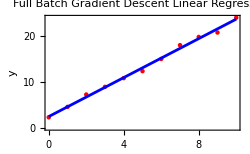

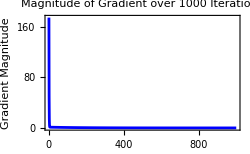

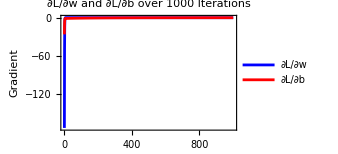

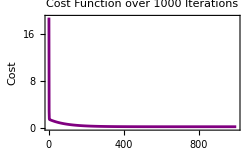

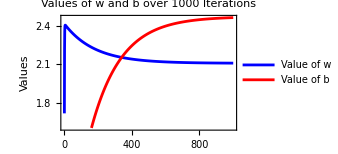

-Graphics3D-

```mathematica
Clear[x,y,w,b];

costFunction[x_,y_,w_,b_]=(y-(w*x+b))^2;

costGradient[x_,y_,w_,b_]=D[costFunction[x,y,w,b],{{w,b}}];

fullBatchGradientDescent[data_,initialGuess_,learningRate_,iterations_]:=Module[
{w=initialGuess[[1]],b=initialGuess[[2]],n=Length[data],gradientList={},costList={},wValues={},bValues={}},
Do[
gradients=(1/Length[data])*Total[costGradient[#[[1]],#[[2]],w,b]&/@data];
gradientList=Append[gradientList,gradients];

w-=learningRate*gradients[[1]];
b-=learningRate*gradients[[2]];
AppendTo[wValues,w];
AppendTo[bValues,b];

costs=(1/Length[data])*Total[costFunction[#[[1]],#[[2]],w,b]&/@data];
costList=Append[costList,costs],
{iterations}
];
{w,b,gradientList,costList,wValues,bValues}
];

data=Table[
{x,2*x+3+RandomReal[{-1,1}]},
{x,0,10}];

initialGuess={0.,0.};
learningRate=0.01;
iterations=1000;
{finalW,finalB,gradientList,costList,wValues,bValues}=fullBatchGradientDescent[data,initialGuess,learningRate,iterations];

errors=Flatten[
Table[
{w,b,(1/Length[data])*Total[costFunction[#[[1]],#[[2]],w,b]&/@data]},
{w,0,4,0.1},
{b,0,4,0.1}
],
1];

Print["Final values: w = ",finalW,", b = ",finalB];

Show[
ListPlot[
data,
PlotStyle->Red,
PlotLegends->Placed[{"Data"},{0.55,0.1}],
ImageSize->250
],
Plot[finalW*x+finalB,
{x,0,10},
PlotStyle->Blue,
PlotLegends->Placed[{"Regression Line"},{0.55,0.1}],
ImageSize->250
],
Frame->True,
FrameLabel->{"x","y"},
PlotLabel->"Full Batch Gradient Descent Linear Regression"
]

ListLinePlot[
Norm/@gradientList,
PlotStyle->Blue,
Frame->True,
FrameLabel->{"Iterations","Gradient Magnitude"},
PlotLabel->"Magnitude of Gradient over 1000 Iterations",
PlotRange->All,
ImageSize->250
]

gradientWList=gradientList[[All,1]];
gradientBList=gradientList[[All,2]];

ListLinePlot[
{gradientWList,gradientBList},
PlotStyle->{Blue,Red},
Frame->True,
FrameLabel->{"Iterations","Gradient"},
PlotLegends->Placed[{"∂L/∂w","∂L/∂b"},{0.70,0.4}],PlotLabel->"∂L/∂w and ∂L/∂b over 1000 Iterations",
PlotRange->All,
ImageSize->250
]

ListLinePlot[
costList,
PlotStyle->Purple,
Frame->True,
FrameLabel->{"Iterations","Cost"},
PlotLabel->"Cost Function over 1000 Iterations",
PlotRange->All,
ImageSize->250
]

ListLinePlot[
{wValues,bValues},
PlotStyle->{Blue,Red},
Frame->True,
FrameLabel->{"Iterations","Values"},
PlotLegends->Placed[{"Value of w","Value of b"},{0.75,0.4}],
PlotLabel->"Values of w and b over 1000 Iterations",
ImageSize->250
]

Show[
ListPlot3D[
errors,
PlotLegends->Automatic,
ColorFunction->"Rainbow",
PlotRange->Full,
PlotLabel->"Cost Function Surface and Updates \n of (w,b,cost) Over 1000 Epochs",
AxesLabel->{"w","b","Cost"},
ImageSize->250
],
ListLinePlot3D[
Transpose[{wValues,bValues,costList}],
PlotStyle->Directive[Opacity[0.5],Red],
AxesLabel->{"w","b","Cost"},
PlotRange->Full,
ImageSize->250
]
]
```